# Enter title here

## Enter subtitle here

Enter subsubtitle here

Enter author here

Enter department here

Enter date here

```mathematica
Quit[]
```

```mathematica
points = {{1,1}, {2,3}, {3,5}, {4,8}}
```

{{1,1},{2,3},{3,5},{4,8}}

```mathematica
poly[x_] = InterpolatingPolynomial[points, x]
```

1+(2+1/6 (-3+x) (-2+x)) (-1+x)

```mathematica
logistic[x_, k_, a_] := a / (1+Exp[-k*x])
k = 0.1;
a = 100;
```

```mathematica
scaledPoly[x_] = logistic[poly[x], k, a]
lastPointPoly = poly[Length[points]]
firstPointLogistic = scaledPoly[Length[points]]
diff = firstPointLogistic - lastPointPoly
scaledPoly[x_] = logistic[poly[x], k, a]-diff
```

100/(1+ⅇ^(-0.1 (1+(2+1/6 (-3+x) (-2+x)) (-1+x))))

8

68.9974

60.9974

-60.9974+100/(1+ⅇ^(-0.1 (1+(2+1/6 (-3+x) (-2+x)) (-1+x))))

```mathematica
combined[x_] :=Piecewise[{{poly[x], x <= Length[points]}, {scaledPoly[x], x > Length[points]}}]
```

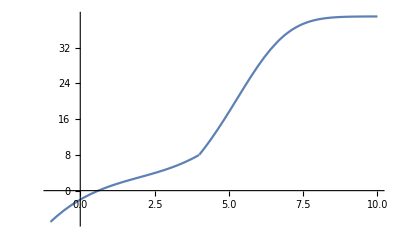

```mathematica
Plot[combined[x], {x, -1, 10}]
```